```mathematica
ClearAll["Global`*"]
```

### Choosing a potential and making an SOS

To use: 1) Make sure En or En-Vwell is properly in place, depending if you want peaks or holes; 2) Define V[x,y] using the SOS IC’s section (this may produce errors, ignore them); 3) Choose saddlePts[[1]] or [[2]] as appropriate, then run the minPt, saddlePt code, then run the appropriate fitEq code, then run the trenchYofX code and the associated plot (or for single bump, set the trivial trench in place of this step); 4) Run the SOS IC’s section again, then proceed to simulation; 5) After simulation, make sure the final plot has the correct labels (x vs. s) and energy

#### Triple bump: find saddle, min, and trench (using simple analytical trench, not “better” polynomial fit)

{{-0.703329,-0.880113},{-0.699974,0.16439},{0.298244,-0.856956},{0.323935,0.225554}}

4 extrema in unit cell

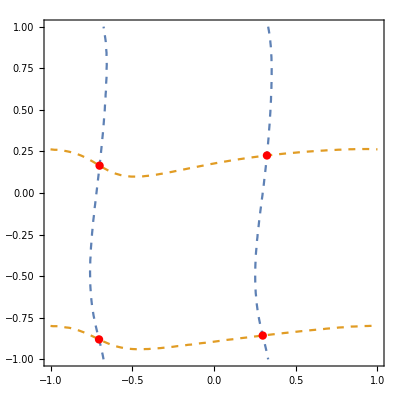
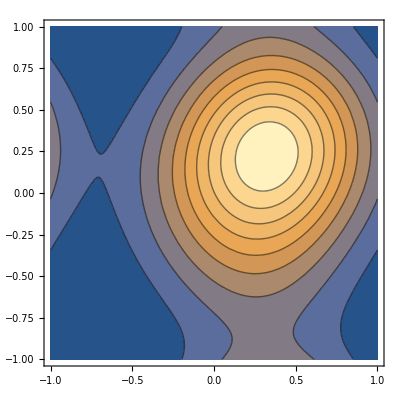

{{-0.699974,0.16439},{0.298244,-0.856956}}

{-0.703329,-0.880113}

```mathematica
(*Define V[x,y] before using*)
FindCrossings2D[{f_,g_},{x_,xmin_,xmax_},{y_,ymin_,ymax_}]:={x,y}/.(FindRoot[{f[x,y]==0,g[x,y]==0},{{x,#[[1]]},{y,#[[2]]}}]&/@(ContourPlot[{f[x,y]==0,g[x,y]==0},{x,xmin,xmax},{y,ymin,ymax}][[1,1]]))
fn[x_,y_]:=(D[V[x,y],x]//Evaluate)
gn[x_,y_]:=(D[V[x,y],y]//Evaluate)
extremaPts=FindCrossings2D[{fn,gn},{x,-a,a},{y,-a,a}]//Select[DeleteDuplicates[Round[#,10.^-10]],-a<#[[1]]<a&&-a<#[[2]]<a&]&//Select[#[[2]]>-0.2a||#[[2]]<-0.5a&](*last Select is a hack, forces removal of specfic bad extrema*)
Print[Length[extremaPts]," extrema in unit cell"]
cp=ContourPlot[{fn[x,y]==0,gn[x,y]==0},{x,-a,a},{y,-a,a},Epilog->{AbsolutePointSize[6],Red,Point/@extremaPts},ContourStyle->Dashed];
cpPot=ContourPlot[V[x,y],{x,-1,1},{y,-1,1}];
{cp,cpPot}
V[{x_,y_}]:=V[x,y]
saddlePts=Select[extremaPts,!MemberQ[{Min[V/@extremaPts],Max[V/@extremaPts]},V[#]]&]
Clear[saddlePt](*saddlePt=saddlePts[[1]]*)
minPt=Select[extremaPts,V[#]==Min[V/@extremaPts]&][[1]]
```

Canceled the use of a numerical “unique” trench solution (see minimized), turns out it’s not necessary. Instead just using Linda’s simple, analytical dV/dy=0

```mathematica
(*dl=Norm[saddlePt-minPt]/10000;
pt=saddlePt+{-dl,0};
trenchPts={saddlePt,pt};
While[Norm[minPt-pt]>dl,
gr=(Grad[V[x,y],{x,y}]//Evaluate)/.{x-> pt[[1]],y->pt[[2]]};
pt+=-gr/Norm[gr]*dl;
AppendTo[trenchPts, pt];
]
AppendTo[trenchPts,minPt];

lp=ListPlot[trenchPts,PlotRange->{{-a,a/2},{-a,-a/2}},AspectRatio->1/3];
fitEq[x_]=Fit[trenchPts,Table[x^n,{n,0,9}],x];
fitp=Plot[fitEq[x],{x,minPt[[1]],saddlePt[[1]]},PlotStyle->{Red,Dashed}];
Show[lp,fitp,cp]*)
```

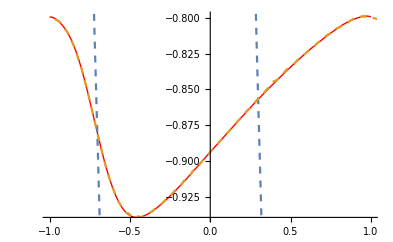

```mathematica
(*Define V[x,y] before using*)
xTstart=-a;
xTend=a;
nPoints=1000;
trenchPts=
Table[
{x0,
y0/.FindRoot[Evaluate[D[V[x0,y],y]]==0/.y->y0,{y0,minPt[[2]]}]}
,{x0,x1=xTstart,x2=xTend,(x2-x1)/nPoints}];
lp=ListPlot[trenchPts];
fitEq[x_]=Fit[trenchPts,Join[(*Table[x^n,{n,0,11}],*)Table[Sin[n x],{n,0,9}],Table[Cos[n x],{n,1,9}]],x];
fitp=Plot[fitEq[x],{x,xTstart,xTend},PlotStyle->{{Red,Thick}}];
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-a,2a},{y,-2a,a},Epilog->{AbsolutePointSize[6],Red,Point/@extremaPts},ContourStyle->Dashed];
Show[fitp,cp]
```

```mathematica
(*trench def.s, borrowed from my Horsley-reproducing code*)
(*need to switch minPt<->saddlePt usage if going between upright and inverted lattices*)
Clear[trenchYofX,trenchSofX,dtrench]
trenchYofX[x_?NumericQ]:=fitEq[x]
maxLength=ArcLength[trenchYofX[x0],{x0,xTstart,xTend},Method->{"NIntegrate"}];
trenchSofX[x_?NumericQ]:=-a+ArcLength[trenchYofX[x0],{x0,xTstart,N[x]},Method->{"NIntegrate"}]/maxLength*2a
trenchSofXmod=Interpolation[Table[{x,trenchSofX[x]},{x,-a,a,2a/100}]];
dtrench[x_]:=(D[fitEq[x],x]//Evaluate)
trenchYofXbounded[x_?NumericQ]:=
Piecewise[{{fitEq[x],xTstart≤x≤xTend}},10^100](*"default" value of 10^100 (outside of range) hopefully not attainable, but won't be relevant in main code anyway due to restriction minPt<x[root]<saddlePt*)
```

InterpolatingFunction::dmval: Input value {-1.09996} lies outside the range of data in the interpolating function. Extrapolation will be used.

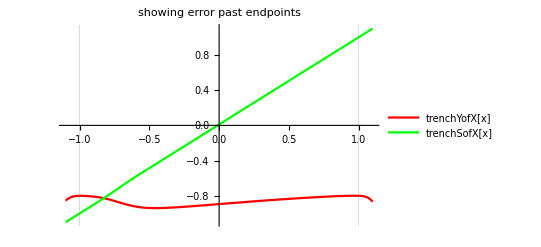
{0.146988,-Graphics-}

```mathematica
(*trenchSofXmod2[x_]:=x(*when ArcLength fails*)*)
Plot[{trenchYofX[x],trenchSofXmod[x]},{x,xTstart-0.1a,xTend+0.1a}(*,PlotRange->{{-1,0.5},{-0.9,-0.7}}*), PlotLabel->"showing error past endpoints",GridLines->{{xTstart,xTend},{}},PlotLegends->{"trenchYofX[x]","trenchSofX[x]"},PlotStyle->{{Red,Thick},Green}]//Timing
```

```mathematica
ColorData[97,"ColorList"]
{ColorData[97,"ColorList"][[2]],
ColorData[97,"ColorList"][[3]]}//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.880722, 0.611041, 0.142051], RGBColor[0.560181, 0.691569, 0.194885]}

#### Single Bump: set trivial trench

Only need to change trenchYofX: a for upright, 0 for inverted; and the axis labels to x and px/√E(or √(E-Vwell))

```mathematica
xTstart:=-a;
xTend:=a;
trenchYofX[x_?NumericQ]:=If[bumpQ,a,0]
trenchSofX[x_?NumericQ]:=x (*range of s is [0,2a]*)
trenchSofXmod=Interpolation[Table[{x,trenchSofX[x]},{x,-2a,2a,4a/1000}]];(*make -2a to 2a to ensure endpoints -a and a are covered okay*)
(*should match trenchSofXmod expression used for triple bump case*)
dtrench[x_]:=0
saddlePts={{0,a},{a,0}};
```

#### Make potential + section line plot

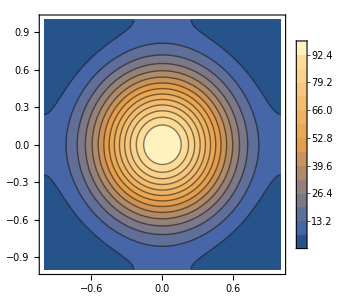

```mathematica
cpPot=ContourPlot[V[x,y],{x,-a,a},{y,-a,a},ImageSize->300,Contours->14,PlotLegends->Automatic,PlotRange->Full];
tp=Plot[{-3,-1,1,3}(*trenchYofX[x]*),{x,-3a,3a},PlotStyle->Red];
Show[cpPot(*,tp*),LabelStyle->16]
```

Poincaré Surfaces of Section (SOS)

To start: Run this first, then run trench code above based on number of bumps, then run this again

```mathematica
prec=MachinePrecision;

(* Change bumpQ for bumps vs holes; True means bumps, False means holes *)
bumpQ=True;
numBumpOrHole=1;

(* repeat V definition for convenience *)
(* will get shifted below so that Vmin=0.0 *)
If[numBumpOrHole==1,
V[x_,y_]:=If[bumpQ,1,-1]*U0((EllipticTheta[3,-(π x)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π y)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)-V0)
,(*else ==3 presumably*)

V[x_,y_]:=
If[bumpQ,1,-1]*U0((EllipticTheta[3,-(π x)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π y)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)+4(EllipticTheta[3,-(π (x-1/√7))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π (y-1/√11))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)+(EllipticTheta[3,-(π (x-1/√13))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π (y+1/√5))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)-V0)
];

(* use constants A[[n]] to force small coupling terms and check that SOS is mostly tori -- if not, noise could be present.
want: Subscript[A, mn]=0.1 for all coupling terms, =1 for non-coupling terms
strategy: rewrite EllipticTheta's in V[x,y] as a combined double sum, so that Subscript[A, mn] can be defined explicitly *)
(*nmax=3;
(* going from def: θ3[x_]:=Sum[Exp[(-π^2 ϵ^2 n^2)/(2 a^2)]Cos[(pi x n)/a],{n,-nmax,nmax}] *)
V[x_,y_]:=If[bumpQ,1,-1]*U0(Sum[ Sum[A[[m+nmax+1,n+nmax+1]]Exp[(-π^2 ϵ^2 m^2)/(2 a^2)]Cos[(π x m)/a]Exp[(-π^2 ϵ^2 n^2)/(2 a^2)]Cos[(π y n)/a],{n,-nmax,nmax}],{m,-nmax,nmax}]/(4 a^2)-V0)
A=Table[Table[If[],{m,-nmax,nmax}],{n,-nmax,nmax}];(* A(-nmax,-nmax) is technically A[[1,1]], A(0,0) is A[[nmax+1,nmax+1]], and so on *)
Print["A=",A//MatrixForm]*)

(* resonance analysis H *)
(* ways to ensure canonical variables: 
- 1. if using cos^2(x), then lattice constant a is clearly π/2 not 1. however the assumption (a=1) has permeated pretty thoroughly in my code, it may be difficult to dig it out and correct it. pro -- it matches my analysis notation.
- 2. if using cos^2(π/2*x), then a=1 but H= (2/π*px)^2+... . then the equations of motion need to account for this, plus the values px and py are given, and the rule calculating py from the other variables. that's very scattered throughout my code.
- 3. if using unscaled H (cos^2(π/2*x) but px^2, V1 instead of u1) then (a=1) and px is normal. but need to use an Hx that is scaled compared to that in my resonance analysis. this seems like the easiest change to make -- no major code change, just carefulness interpreting the results.
- note that third option (scale Hx) should look same as my most naive approach (just changing x->π/2*x and hoping for the best), but just causes U0 to be π^2/4 larger than it would've been to achieve (Vmax=100). So if the shape of V[x,y] is right and Vmax is right then SOS should come out correct.

Conclusion: V[x,y] is scaled by π^2/4 to make (x,p) canonical while maintaining (a=1).
*)

(*nmax=1;
V[x_,y_]:=U0/4(1+2 Sum[Exp[-n^2 π^2 ϵ^2/2]Cos[n π x],{n,1,nmax}])(1+2 Sum[Exp[-m^2 π^2 ϵ^2/2]Cos[m π y],{m,1,nmax}])-U0 V0*)

(*U0 Exp[-π^2ϵ^2/2](1-2Sum[Exp[-q^2 π^2 ϵ^2/2],{q,1,nmax}])(Cos[x π/2]^2+Cos[y π/2]^2)+Sum[4 U0 Exp[-(m^2+n^2)π^2 ϵ^2/2] Cos[m x π/2]^2 Cos[n y π/2]^2,{m,1,nmax},{n,1,nmax}](* -- outdated but was used for HQ ϵ=0.7 plots among others. used V0=Subscript[θ, 3][x=1]Subscript[θ, 3][y=1]/4. *)
*)
V[{x_,y_}]:=V[x,y]

(* set main parameters *)
ϵ=SetPrecision[0.7,prec];
a=SetPrecision[1.0,prec];

U0=1.;(*placeholder, see below*)
V0=0;(*placeholder, see below*)

(* find correct V0 and U0 *)
Vmax=100;(*desired, determines U0*)
V0=Minimize[V[x,y]/U0,{x,y}][[1]];
U0=Vmax/Maximize[V[x,y],{x,y}][[1]];

(*Vmin=-100;(*desired, determines U0*)
V0=-1*Maximize[V[x,y]/U0,{x,y}][[1]];
U0=Vmin/Minimize[V[x,y],{x,y}][[1]];*)

(* check Vmax is same as desired (see above) and Vmin is zero *)
Print["V_max=",Maximize[V[x,y],{x,y}][[1]]," (=",Vmax,"?)"]
Print["V_min=",Vmin=Minimize[V[x,y],{x,y}][[1]]," (=",0,"?)"]

(*Print["V_max=",Maximize[V[x,y],{x,y}][[1]]," (=",0,"?)"]
Print["V_min=",Minimize[V[x,y],{x,y}][[1]]," (=",Vmin,"?)"]*)

Print["Using U0=",U0,", V0=",V0]

(* get saddle potentials, depends on getting correct saddlepts first *)
Print["V_(saddle - 1)=",Vsaddle1=V[saddlePts[[1]]]]
Print["V_(saddle - 2)=",Vsaddle2=V[saddlePts[[2]]]]

(* set energy and time *)
En=SetPrecision[1,prec]; (* should often be overidden by xmax method below or by EnList *)
(* precision=∞; note evaluating x[t] depends on precision of t, so always keep t exact via dt and tmax *)
dt=Rationalize[0.2];(* should sometimes be overridden by lyapunov stuff below *)

(*(* change En<->En-Vwell here when going upright<->inverted *)
Npxi=5;
Nxi=5;
dpxi=2Floor[√EnMod,10^-14]/Npxi;(* for EnList calcs, this is overwritten in Main code for each En *)
xstart:=xTstart;
xend:=xTend;
dxi:=(xend-xstart)/Nxi;*)

(*Print["numICs=",numICs=((xend-xstart)/dxi+1)*(2√EnMod/dpxi+1)]*)
```

V_max=100. (=100?)

V_min=0. (=0?)

Using U0=561.129, V0=0.168895

V_(saddle - 1)=41.0916

V_(saddle - 2)=41.0916

```mathematica
saddlePts
```

{{0,1.},{1.,0}}

```mathematica
(*(* integrable version -- must be evaluated after V0,U0,etc to ensure the coupling terms are treated as a perturbation *)
V[x_,y_]:=U0(1/(4 a^2)(EllipticTheta[3,(π x)/(2a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))]+EllipticTheta[3,(π y)/(2a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))]-1)-V0)
Vmax=Maximize[V[x,y],{x,y}][[1]]*)
```

74.9385

```mathematica
V[x,y]//Expand
```

31.0731+18.9269 Cos[π x]+18.9269 Cos[π y]+31.0731 Cos[π x] Cos[π y]

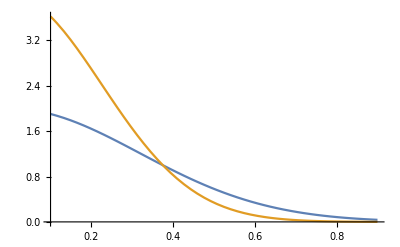

```mathematica
(* V1 versus V2 *)
Plot[{2Exp[-π^2 ϵ0^2/2],4Exp[-π^2 ϵ0^2]},{ϵ0,0.1,0.9}]
```

```mathematica
Plot3D[V[x,y],{x,-1,1},{y,-1,1},PlotRange->All,LabelStyle->16,ColorFunction->"M10DefaultDensityGradient"]
```

-Graphics3D-

For configuration space plotting

```mathematica
trenchXofS[s_]:=InverseFunction[trenchSofX][s]
```

```mathematica
(*choices of xstart and pxstart are where I'm guessing the fixed point (or periodic orbit) is; use guess and check below*)
xstart=(*trenchXofS[0.577]*)1.25
xend=xstart;
dxi=1;

pxstart=(*-0.207*√EnMod*)0.1
pxend=pxstart;
dpxi=1;
```

1.25

0.1

```mathematica
(*check the corresponding (s,ps) for the above (xstart,pxstart); use guess and check to get xstart and pxstart to correspond to the correct point in an SOS*)
sOrbit=trenchSofX[xstart]
θ1=ArcTan[dtrench[xstart]];
pystart=√(En-V[xstart,trenchYofX[xstart]]-pxstart^2);
θ2=ArcTan[ If[pxstart==0,∞,pystart/pxstart]]+If[pxstart<0,π,0]; (*second term corrects for Arctan limited range*)
p=√(pxstart^2+pystart^2);
psOrbit=p Cos[θ2-θ1];
psOrbit/√EnMod
```

1.93941

-0.0286322

To get comparable SOS’s for different parameter values:
solve for xmaxOverA (= percent of x values that are impossible) for one set of parameters, change parameters, then find En given that xmaxOverA and use it in the new set

```mathematica
xmaxOverA=(x/.Solve[En==V[x,yn],x])[[1]]/a
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-0.603594

```mathematica
En=V[xmaxOverA*a,yn]
dpxi=2√En/25;
dxi=2a/50;
numICs=2a/dxi*(2√En/dpxi+1)
```

-4.66404+10.7982 EllipticTheta[3,-1.5708 xmaxOverA,0.291213]

1300.

TEST for skippedICs and total ICs

```mathematica
(*accurate method*)
skippedICs=0;
pointsTest=Table[
Table[
If[Abs[pxi]^2>En-V[xi,fitEq[xi]],Null, 0,Null]
,{xi,xstart,xend,dxi}]
,{pxi,-√EnMod,√EnMod,dpxi}];
skippedICs=Length[Select[Flatten[pointsTest,2],#===Null&]]
numICs-skippedICs
```

```mathematica
foo={{0.1,0.1},{1,1},{0.1,0.1},{2,2}}
DeleteDuplicates[foo]
```

{{0.1,0.1},{1,1},{0.1,0.1},{2,2}}

{{0.1,0.1},{1,1},{2,2}}

```mathematica
xpxList
```

{{-0.46,3.7},{-0.45,3.7},{-0.44,3.7},{-0.43,3.7},{-0.42,3.7},{-0.41,3.7},{-0.46,2.7},{-0.45,2.7},{-0.44,2.7}}

#### Main Calculation

Requires a change at FindRoot for 3-Peak vs 1-Peak and Bump vs Well

```mathematica
Vsaddle1
```

8.07752

```mathematica
Clear[En]
EnList=SetPrecision[Table[en,{en,{100}}],prec];
EnModList=Table[EnList[[j]]-If[bumpQ,0,Vmin],{j,Length@EnList}];

skippedICs={};

Nxi=15;
Npxi=30;

tmax=10;

Clear[x0,px0,y0,py0,xi0,pxi0,yi0,pyi0,x,y,px,py,x1,y1,t,t0,xSample,pxSample];
pointsArray=(*Parallel*)Table[
(*Print["En=",En];*)
EnMod=If[bumpQ,En,En-Vmin];
(* EnMod should always be positive, En should be physically true (sometimes negative) *)

(*Module[{dpxi=2N[Floor[√EnMod,10^-14]]/Npxi},(*for ParallelTable*)*)

Clear[sampled,testAbort,abortNow];
testAbort=False; (* if True, will ABORT after first IC *)
sampled=False; (* do not change *)
abortNow=False; (* do not change *)

Clear[xSample,pxSample];

(*(* grid ICs -- see Nxi, Npxi above*)
dxi=2a/(Nxi);
pxMax=N@Floor[√EnMod,10^-14];
dpxi=2pxMax/(Npxi-1);
xpxList=Flatten[Table[{xn,pxn},{xn,-a,a-dxi,dxi},{pxn,-pxMax,pxMax,dpxi}],1];*)

(*{xSample,pxSample}=(*xpxList[[Round[Length@xpxList/2]]];*)
Select[xpxList,En-Abs[#[[2]]]^2≥V[#[[1]],trenchYofX[#[[1]]]]&][[1]];*)

(*(* one IC *)
numICs=1;
xSample=SetPrecision[0.1745,prec];
pxSample=SetPrecision[0.908(*0 √EnMod*),prec];
xpxList={{xSample,pxSample}};*)

(* a set of ICs *)
(*xpxList=Flatten[Join[
Table[{j,k},{j,{-0.22,-0.24}},{k,{-4,4}}],
{}],1];*)
xpxList=Flatten[Join[
(*Table[{{0.,dpx}},{dpx,0.001,0.002,0.001}],*)
(*Table[{sgn(0.039+dx),1.05},{dx,{0.008,0.016,0.023}},{sgn,{1,-1}}],*)
(*Table[{{dx,0}},{dx,0.09,0.16,0.02}],*)
Table[{0.1772+dx,sgn*0.925},{dx,0.005,0.02,0.005},{sgn,{1,-1}}],
Table[{0.+dx,sgn*2.666},{dx,0.025,0.075,0.025},{sgn,{1,-1}}](*,
{0.294,0},{0.42,3.45},{0.261,4.94},{0.56,5.75}*)
],1];

(*Δ=10^-4;
xpxList=Table[{t (*Exp[Abs@t/(10^-8)]*),15.95t (*Exp[Abs@t/(10^-8)]*)},{t,-Δ,Δ,Δ/10}];
(*Δ=10^-10;
xpxList=Table[{t Exp[Abs@t/(10Δ)],17.7446t Exp[Abs@t/(10Δ)]},{t,-50Δ,50Δ,Δ/100}];(* works well at E=100.001, I think *)*)*)

(* only for a set of ICs *)
numICs=Length@xpxList;
{xSample,pxSample}=xpxList[[2]];(*for config space viewing*)


If[En==EnList[[1]],
Print["numICs=",numICs=Length@xpxList](* this numICs won't count if parallel *)
];

points=ParallelTable[
{xi,pxi}=xpxpair;(* necessary for using xpxpair *)

Clear[x,px,y,py,sol,s,ps,ptrans];
yi=trenchYofX[xi];(*starting on SOS*)
(*yi=0;          (*!TEMPORARY!*)*)

(*Print["debug:",En,",",Abs[pxi]^2,",",V[xi,yi]]; (*debug*)*)
If[En-Abs[pxi]^2<V[xi,yi],Null, (*throw out unphysical cases*)(*TESTING!!*)
(*Print[{xi,pxi,yi,pyi}];*)

Clear[pyi];
pyirules=Solve[pxi^2+pyi^2+V[xi,yi]==En,pyi];(*,WorkingPrecision->highPrec*)
pyi=Chop[Evaluate[pyi/.pyirules[[2]]],10^-15]; (*Using [[2]] because it has pyi>0*)

eqnx=x'[t]==2px[t];
eqnpx=px'[t]==-D[V[x[t],y[t]],x[t]];
eqny=y'[t]==2py[t];
eqnpy=py'[t]==-D[V[x[t],y[t]],y[t]];

sol1=NDSolve[{eqnx,eqnpx,eqny,eqnpy,x[0]==xi,px[0]==pxi,y[0]==yi,py[0]==pyi},{x,px,y,py},{t,0,tmax},MaxSteps->10000000,MaxStepSize->0.001(*,WorkingPrecision->prec-1*)];(* SMALL ϵ or E=Vmax => use MaxStepSize *)
sol=sol1[[1]];

x1[t_]=Evaluate[x[t]/.sol];
y1[t_]=Evaluate[y[t]/.sol];

x[t_]=Mod[Evaluate[x[t]/.sol],2a,-a];
px[t_]=Evaluate[px[t]/.sol];
y[t_]=Mod[Evaluate[y[t]/.sol],2a,-a];
py[t_]=Evaluate[py[t]/.sol];

roots={};
For[t0=0,t0<tmax,t0=t0+dt,
Quiet[  (*CHANGE FOR 3-PEAK VS 1-PEAK AND BUMP VS WELL*)
root=FindRoot[
Abs@(* for bump *)
y[t]-Abs@Mod[trenchYofX[x[t]],2a,-a]==0 (* repeat below *)
,{t,t0}(*,WorkingPrecision->Precision@y[t0]*)];
t1=Evaluate[t/.root];

If[(*t0-dt/2≤t1<t0+dt/2 &&*)t1≥0&&t1≤ tmax
&&Round[Abs@y[t1]-Abs@Mod[trenchYofX[x[t1]],2a,-a],10^-2 a]==0,(* copy from above, add Round, and change t->t1 *)
AppendTo[roots,Chop[t1]]]
]
];
roots=Sort[DeleteDuplicates[roots,#1==#2&]];

(*sample for debugging*)
If[{xi,pxi}=={xSample,pxSample},
(*If[!sampled&&NoneTrue[{xi-xstart,Round[pxi+√EnMod,10^-10]},#==0&],*)(*take first IC that isn't at minimum or moving horizontally/vertically*)

(*x0[t_]=x1[t];px0[t_]=px[t];y0[t_]=y1[t];py0[t_]=py[t];*)
x0[t_]=x[t];px0[t_]=px[t];y0[t_]=y[t];py0[t_]=py[t];
xi0=xi;pxi0=pxi;yi0=yi;pyi0=pyi;roots0=roots;
sampled=True;
abortNow=testAbort;
];
If[abortNow,Abort[]];

pointsPart={};
For[i=1,i≤Length[roots],i++,
(*If[Chop[Re[py[roots[[i]]]]]>0,(*only use py>0 to avoid a mirror image*)
AppendTo[pointsPart,{Chop[Re[x[roots[[i]]]]],Chop[Re[px[roots[[i]]]]]/√En}];
];*)
(*borrowed from my Horsley-reproducing code*)
t1=roots[[i]];
s=trenchSofXmod[x[t1]];(*CAREFUL about what SofX function is here*)
θ1=ArcTan[dtrench[x[t1]]];
θ2=ArcTan[ If[px[t1]==0,∞,py[t1]/px[t1]]]
+If[px[t1]<0,π,0]; (*second term corrects for Arctan limited range*)
p=√(px[t1]^2+py[t1]^2);
ps=p Cos[θ2-θ1];
ptrans=p Sin[θ2-θ1];
(*Print[{"1:",ptrans,s,t1}];*)
If[ptrans>0,
(*Print[{"2:",ptrans,s,t1}];*)
AppendTo[pointsPart,{s,ps(*/√EnMod*)}];
]
];
pointsPart

,Null]
(*,{xi,xstart,xend,dxi}
,{pxi,-Floor[√EnMod,10^-14],Floor[√EnMod,10^-14],dpxi}];//Timing//AbsoluteTiming;*)(* Floor avoids pxi^2>En due to precision issues *)
,{xpxpair,xpxList}];//Timing//AbsoluteTiming;

Print["Finished E=",En];

pointsOrig=points;
points=Flatten[points,0];(* flatten 0 for xpxpair, 1 for xi,pxi *)
points
,{En,EnList}];//Timing//AbsoluteTiming
Print["skippedICs=",skippedICs=Table[Length[Select[pointsArray[[j]],#===Null&]],{j,1,Length[pointsArray]}]]
pointsArray=Table[Select[pointsArray[[j]],#=!=Null&],{j,1,Length[pointsArray]}];

Print["Abs Timing (minutes) = ",%%%[[1]]/60.]
(*Print["Delay(?) (minutes) = ",(%%[[1]]-%%[[2,1]])/60.]*)
Print["Computation time (per proc?) (minutes) = ",%%%%[[2,1]]/60.](*beware number of % signs here*)
Print["numPoints=",Table[Length@Flatten[pointsArray[[j]],1],{j,Length@pointsArray}]]
```

numICs=14

Finished E=100.

{19.0743,{1.73438,Null}}

skippedICs={0}

Abs Timing (minutes) = 0.317904

Computation time (per proc?) (minutes) = 0.0289063

numPoints={336}

```mathematica
(* use if parallel *)
numICs=Nxi*Npxi;
```

```mathematica
EmitSound[Sound[SoundNote[10,0.2]]]
```

CAREFUL:
- Change labels s,ps <-> x,px for 3 bump <-> 1 bump and Change E<->E-Vwell !!!

```mathematica
tempPA=pointsArray;
```

Compare these two (outputs below) for small tmax, then shift dt to make these close to equal. An extra-small dt isn’t as good as you think! It gets hard-to-find points, but misses some obvious points too (not clear why). You may never get close to perfect though, because different trajectories can have very different ‘appropriate’ dts.

```mathematica
(* how efficient is my dt? *)
points={};
points=Table[Flatten[pointsArray[[j]],1],{j,1,Length[pointsArray]}];(* the number in flatten is nonzero since pointsArray isn't pre-flattened *)
Table[
{Length@points[[j]],
(Floor@(tmax/dt)+1)*(numICs-skippedICs[[j]])} (* maximum possible points *)
,{j,1,Length[points]}]
Map[N@#[[1]]/#[[2]]&,%](* percent of maximum points *)
```

{{101861,127022},{122092,127022}}

{0.801916,0.961188}

```mathematica
(* delete erroneous points -- for y=0 SOS *)
pointsArrayOrig=pointsArray;
Table[
foo=Length@Select[pointsArray[[k]],(#[[2]])^2+V[#[[1]],0]>EnList[[k]]&];
pointsArray[[k]]=Select[pointsArray[[k]],(#[[2]])^2+V[#[[1]],0]≤EnList[[k]]&];
foo
,{k,1,Length@pointsArray}]
```

{16,31,37,38,45,63,47,35,12,0,2}

```mathematica
EmitSound[Sound[SoundNote[10,0.2]]]
```

```mathematica
(* for getting Poincare map SOS *)
pointsMod=Transpose@(#[[1;;2]]&/@Select[pointsArray[[1]],Length[#]>1&]);
```

```mathematica
(* for reducing pointsArray to zoomed in section, to reduce time it takes to plot *)
(*f=2;*)
pointsMod=Select[Flatten[pointsArray[[1]],1],Abs[#[[1]]]≤a/f&&Abs[#[[2]]]≤1.1√EnList[[1]]/f&];
```

```mathematica
multPx[en_,{x_,pxNormed_}]:={x,en*pxNormed}
```

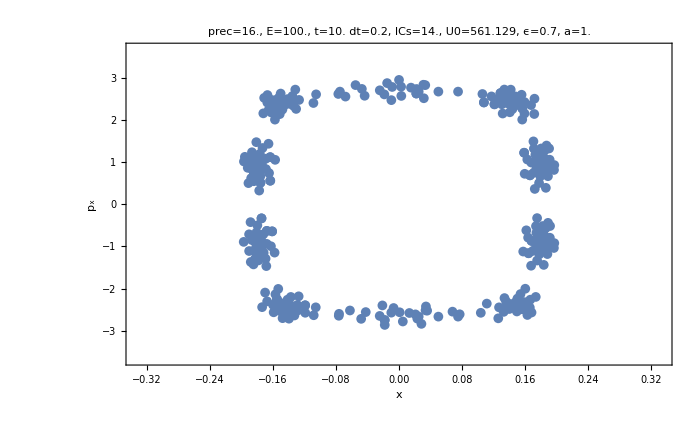

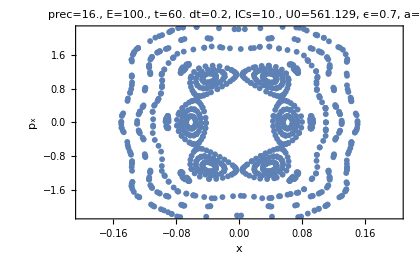

```mathematica
(* Plot SOS *)
f=3;
{xf,pxf}={0,0 √EnModList[[1]]}(*{xSample,pxSample}*);
Table[ListPlot[(*pointsMod*)pointsArray[[j]](*Map[multPx[√EnList[[j]],#]&,pointsArray[[j]],{1}]*),PlotRange->{(*{-0.55a,-0.75a}*){xf-a/f,xf+a/f},(*{0.15 √EnList[[j]],0.35 √EnList[[j]]}*){pxf-1.1√EnModList[[j]]/f,pxf+1.1√EnModList[[j]]/f}},
PlotStyle->{{PointSize[0.01(*0.0001*)],ColorData[97,"ColorList"][[1]](* enforces blue *)}},AxesOrigin->{-a,-√EnModList[[j]](*-1.1*)},PlotLabel->SetPrecision[Row@{"prec=",Round[prec,0.1],", E=",EnList[[j]],", t=",tmax," dt=",dt,", ICs=",numICs-skippedICs[[j]],", U0=",U0,(*", V_max=",Vmax,*)", ϵ=",ϵ,", a=",a},MachinePrecision],Ticks->{True,True},FrameTicksStyle->{Directive[16],Directive[16]},Frame->{True,True,True,True},FrameLabel->{Style["x",16],Style["p_x",16]}(*FrameLabel->{Style[If[numBumpOrHole==1,"x/a","s/a"],16],Style[If[numBumpOrHole==1,If[bumpQ,"p_x/√E","p_x/√(E - Vwell)"],If[bumpQ,"p_s/√E","p_s/√(E - Vwell)"]],16]}*),ImageSize->700],{j,1,Length[pointsArray]}]
```

```mathematica
pointsArray=fooPAtest;
```

```mathematica
fooPAtest=fooPA;
```

```mathematica
fooPAtest[[1]]=Join[fooPA[[1]],pointsArray[[1]]];
```

```mathematica
fooPAtest[[4]]=Join[fooPA[[4]],pointsArray[[1]]];
```

```mathematica
fooPAtest
```

```mathematica
fooPA=pointsArray;
```

```mathematica
(* get IC that would give complementary orbit, e.g. period-1 to complement period-4 *)
roots;
{x0[t],-px0[t],Abs@y0[t],-py0[t]}/.t->roots[[4]]
```

{0.000275154,9.43931,1.,3.30143}

{-0.24,4.,1.,8.79663}

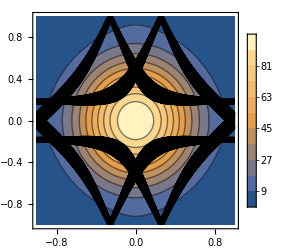

```mathematica
{xi0,pxi0,yi0,pyi0}
cpPot=ContourPlot[V[x,y],{x,-1,1},{y,-1,1},ImageSize->250,Contours->10,PlotLegends->Automatic,PlotRange->Full];
configPlot=ParametricPlot[{x0[t],y0[t]},{t,0,tmax},PlotStyle->Black,MaxRecursion->15];
Show[cpPot,configPlot]
```

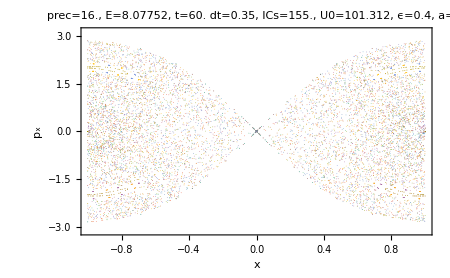
QUESTIONS: 
- Why is the unstable orbit in Sinai stable for much longer (higher E) than the unstable orbit in honeycomb? (Is this answerable? Probably not.)
- If we look at smaller ϵ (0.4 may be fine) where chaos exists near saddle energy, will we find the resonance effect at E=Vsaddle?
	- A: No resonance effect, shown here.
(cont. below plot)
	 -Graphics-
- Does triple peak have the resonance effect? Seems unlikely, since it lacks symmetry.
- Does triple peak have resonance effect at a different energy? Maybe an energy that tends to reflect at 60 degrees instead of 90? (due to geometry of lattice)

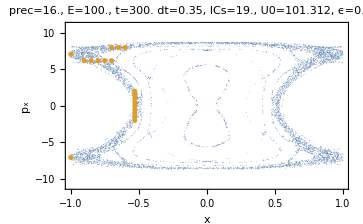

```mathematica
foo={x[t],px[t],y[t],py[t],roots,pointsArray}; (* temp backup *)
```

Saving and Retrieving data

```mathematica
(* saving all data associated with a run *)
SetDirectory["/Users/mollyporter/Documents/UT Austin Stuff/Research (Austin)/Quantum Chaos/data"];

num="001";(* increase *)
descrip="sb_ee=0,7_E=Vmax_fullH";

x>>descrip<>"_"<>"sim"<>num<>"_x.m"
px>>descrip<>"_"<>"sim"<>num<>"_px.m"
y>>descrip<>"_"<>"sim"<>num<>"_y.m"
py>>descrip<>"_"<>"sim"<>num<>"_py.m"
roots>>descrip<>"_"<>"sim"<>num<>"_roots.m"
pointsArray>>descrip<>"_"<>"sim"<>num<>"_pointsArray.m"
```

```mathematica
(* retrieve data -- first set working directory to .../Quantum Chaos/data *)
SetDirectory["/Users/mollyporter/Documents/UT Austin Stuff/Research (Austin)/Quantum Chaos/data"];

num="001";(* specify *)
descrip="sb_ee=0,7_E=Vmax_fullH";(* specify *)

Clear[x,px,y,py]
x=Get@(descrip<>"_"<>"sim"<>num<>"_x.m");
px=Get@(descrip<>"_"<>"sim"<>num<>"_px.m");
y=Get@(descrip<>"_"<>"sim"<>num<>"_y.m");
py=Get@(descrip<>"_"<>"sim"<>num<>"_py.m");
roots=Get@(descrip<>"_"<>"sim"<>num<>"_roots.m");
pointsArray=Get@(descrip<>"_"<>"sim"<>num<>"_pointsArray.m");
(*(* for certain older files *)
x=Get@("sim"<>num<>"_"<>descrip<>"_x.m");
px=Get@("sim"<>num<>"_"<>descrip<>"_px.m");
y=Get@("sim"<>num<>"_"<>descrip<>"_y.m");
py=Get@("sim"<>num<>"_"<>descrip<>"_py.m");
roots=Get@("sim"<>num<>"_"<>descrip<>"_roots.m");
pointsArray=Get@("sim"<>num<>"_"<>descrip<>"_pointsArray.m");*)
```

```mathematica
EnList=SetPrecision[Table[en,{en,{100}}],prec];(* make this match loaded data *)
```

```mathematica
(* finding slopes of eigencurves *)
```

```mathematica
pointsMod=Select[pointsArray[[1]],0.06>#[[1]]>0.03&&1.5>#[[2]]>0&];
```

```mathematica
xf:=0;
pxf:=0;
slopes=Map[(#[[2]]-pxf)/(#[[1]]-xf)&,pointsMod]
```

{16.1263,15.7446,16.1256,17.0845,16.8109,14.6719,16.1281,16.0542,16.4501,16.1986,15.6898,15.9744,17.0778,14.8281,15.4798,14.6119,16.6764,15.2526,14.9127,15.9393,15.6227,16.2046,16.1686,16.433,16.8185,15.6755,15.8542}

```mathematica
Total[slopes]/Length[slopes]
```

```mathematica
(* (0,0) for E=Vpeak, y=1 *)
```

15.9487

```mathematica
(* (0,0) for E~Vpeak (E=100.1), y=0 *)
```

17.7255

```mathematica
(* (0,0) for E~Vsaddle (actually E=9, where Vsd=8.078), y=0 *)
```

5.3519

COMMENT ON ERRONEOUS POINTS FOR E=100: The points that lie outside the ‘allowed’ region don’t come from energy non-conservation (like the ϵ=0.1 issues did), instead they seem to come from a sufficiently slow-travelling trajectory either having lower-quality InterpolatingFunction’s for x, px, etc., or having trouble with FindRoot. Either way, the configuration-space trajectory looks fine, as does the energy, so the points should simply be excluded from the final SOS and not worried about.

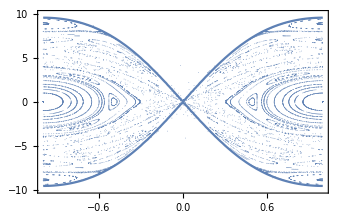

```mathematica
ContourPlot[px^2+V[x,0]==100,{x,-1,1},{px,-10,10},AspectRatio->1/GoldenRatio];
Show[%,foo]
```

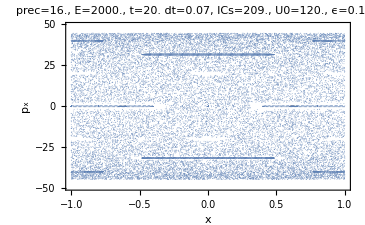

```mathematica
(*SOS for ϵ=0.1*)
```

Counting semi-classical quantum states: J’=nh => J=n(2π)

```mathematica
tpart1=t/.FindRoot[px0[t]==0,{t,0.18}]
tpart2=t/.FindRoot[px0[t]==0,{t,1.25}]
tpart3=t/.FindRoot[px0[t]==0,{t,1.65}]
tpart4=t/.FindRoot[px0[t]==0,{t,2.7}]
```

areaX=48.6941

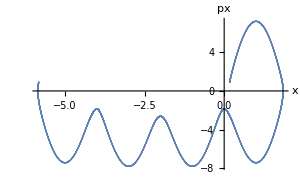

areaY=48.6953

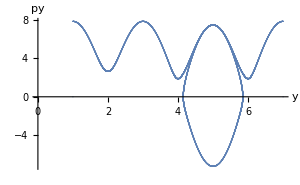

J=97.3894

J/2π=15.5

Remainder=3.14162

```mathematica
(* for CLOSED loops -- find enclosed area *)
ti=0;
tf=roots[[6]];
tnum=10000;
ptsx=Join[
{{x1[ti],0}},
Table[{x1[t],px0[t]},{t,ti,tf,(tf-ti)/tnum}],
{{x1[tf],0}}
];
Graphics`Mesh`MeshInit[];
Print["areaX=",polyAreaX=Abs@PolygonArea[ptsx](*," >2π?"*)]
ListPlot[ptsx,ImageSize->300,AxesLabel->{"x","px"},LabelStyle->16(*,PlotStyle->PointSize[0.01]*)]
ptsy=Join[
{{y1[ti],0}},
Table[{y1[t],py0[t]},{t,ti,tf,(tf-ti)/tnum}],
{{y1[tf],0}}
];
Graphics`Mesh`MeshInit[];
Print["areaY=",polyAreaY=Abs@PolygonArea[ptsy](*," >2π?"*)]
ListPlot[ptsy,ImageSize->300,AxesLabel->{"y","py"},LabelStyle->16]
Print["J=",area=polyAreaX+polyAreaY]
Print["J/2π=",n=area/(2π)]
Print["Remainder=",area-Floor[area/(2π)]*2π]
```

```mathematica
n
```

```mathematica
15.500004130460363
```

```mathematica
roots
```

{0,0.207372,0.44509,0.698857,0.95268,1.19031,1.39767,1.63541,1.88914,2.14295,2.38057,2.58791,2.82562,3.07936,3.33313,3.57079,3.77812,4.01577,4.26955,4.52328,4.761,4.96835,5.20596,5.45978,5.71352,5.95126,6.15863,6.39627,6.65009,6.90387,7.14157,7.34894,7.58665,7.84043,8.09425,8.33189,8.53925,8.77699,9.03073,9.28455,9.52217,9.72952}

```mathematica
x0[#]&/@roots
```

{0.,-0.0000131406,-5.61707×10^-6,0.0000107192,0.0000102321,-6.3541×10^-6,-0.0000129411,8.03562×10^-7,0.0000132884,4.88562×10^-6,-0.0000112101,-9.66597×10^-6,7.04425×10^-6,0.000012701,-1.61396×10^-6,-0.0000133813,-4.1111×10^-6,0.0000116092,9.09514×10^-6,-7.74645×10^-6,-0.0000123915,2.42665×10^-6}

```mathematica
tpart1=t/.FindRoot[px0[t]==0,{t,0.2}]
tpart2=t/.FindRoot[px0[t]==0,{t,1.2}]
```

0.235524

1.16222

0

1.73654

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.4033233086311170979831874916499145911075174808502197265625}. NIntegrate obtained 59.374 and 0.456328 for the integral and error estimates.

areaX=59.374

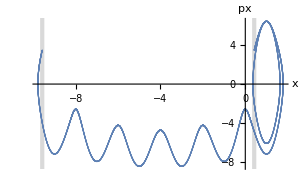

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {8.83188}. NIntegrate obtained 90.6918 and 57.3861 for the integral and error estimates.

areaY=90.6918

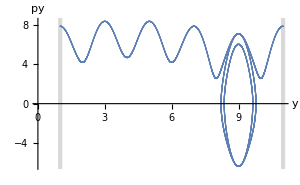

J=97.4695

J/2π=15.5128

Remainder=3.22172

```mathematica
(* for NON-CLOSED or period>1 -- integrate under curve *)
tnum=10000;
tix=0
tfx=roots[[10]]
xi=x1[tix];
xf=x1[tfx];
tiy=tix;
tfy=tfx;
yi=y1[tiy];
yf=y1[tfy];

ptsx=Table[{x1[t],px0[t]},{t,tix,tfx,(tfx-tix)/tnum}];
ptsxPlot=ListPlot[ptsx,GridLines->{{xi,xf},{}},GridLinesStyle->Directive[Thickness[0.01],LightGray],AxesLabel->{"x","px"},LabelStyle->16];
fx=Interpolation[ptsx];
fxPlot=Plot[fx[r],{r,xi,xf},PlotStyle->ColorData[97,"ColorList"][[2]]];
Print["areaX=",areaX=NIntegrate[fx[r],{r,xi,xf}](*," >2π?"*)]
Show[ptsxPlot(*,fxPlot*),ImageSize->300]

ptsy=Table[{y1[t],py0[t]},{t,tiy,tfy,(tfy-tiy)/tnum}];
ptsyPlot=ListPlot[ptsy,GridLines->{{yi,yf},{}},GridLinesStyle->Directive[Thickness[0.01],LightGray],AxesLabel->{"y","py"},LabelStyle->16];
fy=Interpolation[ptsy];
fyPlot=Plot[fy[r],{r,yi,yf},PlotStyle->ColorData[97,"ColorList"][[2]]];
Print["areaY=",areaY=NIntegrate[fy[r],{r,yi,yf}](*," >2π?"*)]
Show[ptsyPlot(*,fyPlot*),ImageSize->300]
(*areaY=areaX;*)

Print["J=",area=(*areaX+areaY*)8.3347+40.3835+0.0160+25.6916+8.3507+14.693]
Print["J/2π=",n=area/(2π)]
Print["Remainder=",area-Floor[n]*2π]
```

```mathematica
(*trenchplot=Plot[trenchYofX[x],{x,-a,a}];*)
Show[cpPot,configPlot,(*trenchplot,*)PlotLabel->SetPrecision[Row@{"Res H, E=",EnList[[1]],", (xi,pxi)=(",xi0,",",pxi0,"),\nn=",n},4]]
```

Track κ_x and κ_y over time for quasiperiodic orbit. Since this lies on resonance, I expect consistently large κ (≈1). This means E_x≈u_1.
I use my resonance analysis H, meaning no higher-order non-coupling terms and nmax=1.
The variables in my simulation are a canonical transformation away from those in my resonance analysis of E=Vmax.

```mathematica
(* factor of 2 due to py>0 for pointsArray *)
Length@roots
Length@pointsArray[[1]]
```

244

122

1

4.59593

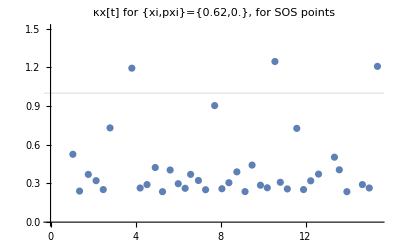

```mathematica
nmax (* nmax=1 was set before simulation, double check here *)
V1=U0 Exp[-π^2 ϵ^2/2](1-2Sum[Exp[-q^2 π^2 ϵ^2/2],{q,1,nmax}]) 
Ex[x_,px_]:=px^2+V1 Cos[π/2 x]^2
κx[x_,px_]:=√(V1/Ex[x,px])
Plot[κx[x0[t],px0[t]],{t,0,10},PlotLabel->Row@{"κx[t] for {xi,pxi}={",xi,",",pxi,"}"},PlotRange->{All,{0,1.5}},GridLines->{{},{1}}];
ListPlot[Table[{t,κx[x0[t],px0[t]]},{t,roots[[;;40]]}],PlotRange->{All,{0,1.5}},GridLines->{{},{1}},PlotLabel->Row@{"κx[t] for {xi,pxi}={",xi,",",pxi,"}, for SOS points"}]
```

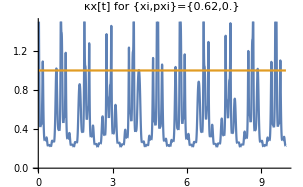
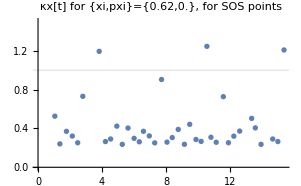
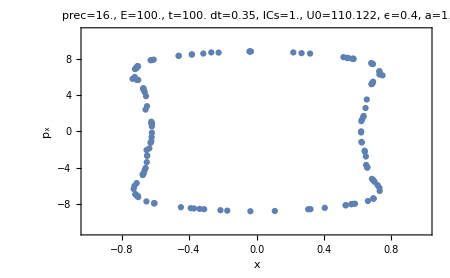

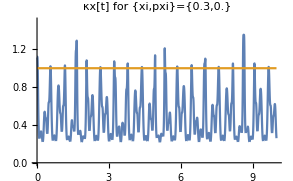
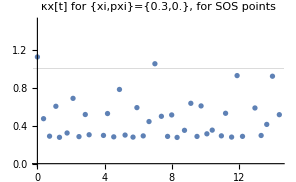
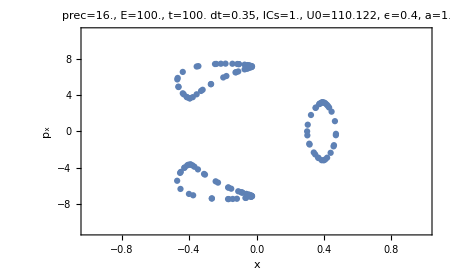

#### Use px0 to determine bounces

Look at px every small time step (<<dt, maybe 0.005), consider two consecutive px that are same within some threshold to be “constant”, and changes from a constant value to be a bounce. It’s okay if the time resolution on when these bounces happen is poor because we care about the total number per time, not when they happen.
- Make sure a transition slope doesn’t count as multiple bounces.
- Don’t include ‘slight’ bounces, in which px may change by ~1

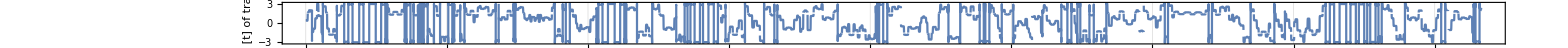

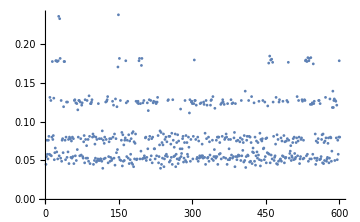

0.0831148

```mathematica
θ[t_]:=Mod[ArcTan[ If[px[t]==0,∞,py[t]/px[t]]]+If[px[t]<0,π,0],2π,-π];

dt0=0.001;(*combo of dt0 and thresh determines level of detail in ListPlot[bounceTimeDifs]*)
θTab=Table[θ[t],{t,0,tmax,dt0}];

(* find spots where bounces occur *)
thresh=0.002;
Table[
If[Abs[θTab[[j-1]]-θTab[[j]]]<thresh&&
Abs[θTab[[j]]-θTab[[j+1]]]>thresh,
j,(*record spot number...*)
-1 (*...or -1*)
]
,{j,2,Length@θTab-1}];
bounceTab=Select[%,#≠-1&];

Map[dt0*#&]@bounceTab;
bounceTimeDifs=Table[%[[j+1]]-%[[j]],{j,1,Length@%-1}];

tEnd=tmax;
Plot[θ[t],{t,0 ,tEnd},GridLines->{Map[dt0*#&]@bounceTab,{}},AspectRatio->1/(GoldenRatio*(tEnd/0.4)),ImageSize->900*tEnd,PlotRange->{{0,Automatic},Automatic},Frame->True,FrameLabel->{None,"Angle θ [t] of trajectory"},LabelStyle->Directive[14],MaxRecursion->10]

ListPlot[bounceTimeDifs,ImageSize->Medium]

(*average time between bounces*)
Mean[bounceTimeDifs]
```

NEXT STEP: Vary initial condition, energies (below and above peak), ϵ. Varying IC will increase precision of given (E,ϵ), while varying E and ϵ gives us context in which to understand high-E, small-ϵ, which should be unique enough to explain its QM-classical inconsistency.

The aim is still to understand why QM doesn’t see high-energy chaos for small ϵ. If the answer is long flight time (multiplied by √E to be ∝ number of unit cells traversed -- think d=v*t => (num unit cells) = √E*(flight time)), then we expect to see larger ((T_flight))_ave*√E for smaller ϵ. If this fails, maybe I want to measure num unit cells traversed more directly somehow? Crossing borders?

Data should be stored as {ϵ, E, ((T_flight))_ave} in the below table.

GUESS:
- Comparing different E’s for ϵ=0.2 won’t be very enlightening. With the threshold for what counts as a bounce set very low, I see no reason to expect bounces to be rarer at high energies -- this would change with a higher threshold, but I’m not sure what determines an appropriate threshold. A low threshold seems appropriate if the question is just how easily chaos appears.
- Comparing different ϵ’s seems useless because bounces are not well-defined for ϵ=0.4.
- But our original question is, “does small ϵ travel many unit cells before bouncing, such that our QM calc’s with only small blocks of unit cells considered manage to miss the chaos entirely?” That’s seeming doubtful to me. Just observing a chaotic trajectory for ϵ=0.2 shows that it often bounces after one or two unit cells, which the QM calc’s should see easily.
- Is there some sense in which it’s not the question of “bounce: yes/no” that matters, but rather, “how much bounce?”? What is very clear is that high-E, small-ϵ makes most bounces fairly small, even if the bounces are just as frequent as other cases.

```mathematica
flightTimeData={};(* only use once *)
```

```mathematica
(* used tmax=50 for all, and ICs near (x,px/√E)=(-0.7,0.979) *)
AppendTo[flightTimeData,{ϵ,EnList[[1]],Mean[bounceTimeDifs]}]
```

{{0.2,1000.,0.0495114},{0.2,2000.,0.0359878},{0.2,500.,0.066045},{0.2,300.,0.0831148}}

{{1000.,0.0495114},{2000.,0.0359878},{500.,0.066045},{300.,0.0831148}}

{{1000.,1.56569},{2000.,1.60942},{500.,1.47681},{300.,1.43959}}

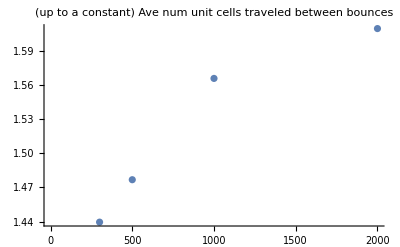

```mathematica
(* !Below plot is probably just an artifact of having a small, finite threshold on what counts as a bounce, meaning at high-E more small bounces are ignored. Or it could be that it's easier to maintain a consistent course for longer at high E. Or these two things are the same. *)
flight0p2=Select[flightTimeData,#[[1]]==0.2&][[;;,{2,3}]]
distVsEn[{en_,t_}]:={en,t √en}(* see discussion further above, num unit cells ~ flight time * momentum *)
Map[distVsEn,flight0p2]
ListPlot[%,PlotLabel->"(up to a constant) Ave num unit cells traveled between bounces"]
```

NEW DIRECTIONS?: How can the presence of chaos at high energies be understood? From one perspective, it’s the large amplitude of high-order cosine terms in the expansion of EllipticTheta. That is, as EllipticTheta gets further from having a small-number-of-terms expansion, it also gets further from integrability. From a QM perspective, we hoped that chaos was being hidden by long flight times between bounces, meaning large N^2-soft billiards required to see it (but this seems unlikely to me). There are however several approximations being made in the QM calc’s: the allowed frequencies nx and ny in the expansion of the wave function u_(ν,k)(r) are limited to -11≤nx≤11; the limits on the N^2-soft billiard (couldn’t find precise numbers on this in the paper); others?

Variation in E = 3.×10^-6

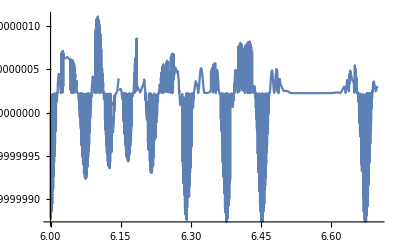

```mathematica
(*checking variation in energy*)
Maximize[{px0[t]^2+py0[t]^2+V[x[t],y[t]],0<t<tmax},t][[1]];
Emax=N[Round[%,10^-6],10];
Minimize[{px0[t]^2+py0[t]^2+V[x[t],y[t]],0<t<tmax},t][[1]];
Emin=N[Round[%,10^-6],10];
Print["Variation in E = ",Emax-Emin]
Plot[px0[t]^2+py0[t]^2+V[x[t],y[t]],{t,6,6.7},PlotRange->All]
```

```mathematica
(*make precision vs time plot*)
```

```mathematica
precTab=Precision/@pointsArray[[1]];
```

```mathematica
ListPlot[Transpose[{roots,precTab}],AxesLabel->{"t","Precision"},LabelStyle->Directive[14],PlotLabel->"Precision of SOS points over time",PlotRange->{{0,20},All},PlotStyle->PointSize[0.01]]
```

#### Triple Bump region of chaos

(See details under single bump, below)

```mathematica
(*find saddles and peak as table of ϵ*)
V0=30.;
a=1.;
ϵ0=ϵ;
Clear[ϵ];(*convenient for plotting as function of ϵ*)
Vth[x_,y_,ϵ_]:=((V0 EllipticTheta[3,-(π x)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π y)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)+4(V0 EllipticTheta[3,-(π (x-1/√7))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π (y-1/√11))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)+(V0 EllipticTheta[3,-(π (x-1/√13))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π (y+1/√5))/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2))
Vth[{x_,y_,ϵ_}]:=Vth[x,y,ϵ]
ϵstart=0.2;
ϵend=1.0;
dϵ=0.02;
ϵlist=Table[ϵ,{ϵ,ϵstart,ϵend,dϵ}];
extremaList=Table[
f[x_,y_]:=(D[Vth[x,y,ϵ],x]//Evaluate);
g[x_,y_]:=(D[Vth[x,y,ϵ],y]//Evaluate);
Join[
Quiet[FindCrossings2D[{f,g},{x,-a,a},{y,-a,a}]]//Select[DeleteDuplicates[Round[#,10.^-10]],-a<#[[1]]<a&&-a<#[[2]]<a&]&//Select[#[[2]]>-0.2a||#[[2]]<-0.5a&],(*last Select is a hack, forces removal of specfic bad extrema*)
Table[{ϵ},4],2]
,{ϵ,ϵstart,ϵend,dϵ}];
Map[Vth,extremaList,{2}];
Vlist=Map[Sort,%];
Vlist=Map[#-Table[#[[1]],Length[#]]&,Vlist];(*subtracting Vmin from all values*)
saddleList1=MapThread[{#1,#2}&,{ϵlist,Map[#[[2]]&,Vlist]}];
saddleList2=MapThread[{#1,#2}&,{ϵlist,Map[#[[3]]&,Vlist]}];
peakList=MapThread[{#1,#2}&,{ϵlist,Map[#[[4]]&,Vlist]}];

ϵ=ϵ0;(*restore ϵ, which we cleared for convenience*)
```

```mathematica
(*plot saddle and peak*)
saddleFit1[x_]=Fit[saddleList1,Table[x^n,{n,0,11}],x];
saddleFit2[x_]=Fit[saddleList2,Table[x^n,{n,0,11}],x];
peakFit[x_]=Fit[peakList,Table[x^n,{n,0,11}],x];(*170/(x+0.1);*)

scaling=0.842;
saddlePeakPlot=Plot[{saddleFit1[x]*scaling,saddleFit2[x]*scaling,peakFit[x]*scaling},{x,0.2,ϵend},PlotRange->All,PlotStyle->{LightGray,Gray,Darker[Gray]},PlotLegends->Placed[LineLegend[{Darker[Gray],Gray,LightGray},{"Peak","High Saddle","Low Saddle"},LabelStyle->Directive[16]],{0.78,0.62}]];
saddlePeakPlot2=ListPlot[{saddleList1*scaling,saddleList2*scaling,peakList*scaling},PlotStyle->PointSize[0.005],PlotStyle->{LightGray,Gray,Darker[Gray]},PlotLegends->Placed[LineLegend[{Darker[Gray],Gray,LightGray},{"Peak","High Saddle","Low Saddle"},LabelStyle->Directive[16]],{0.78,0.62}]];
```

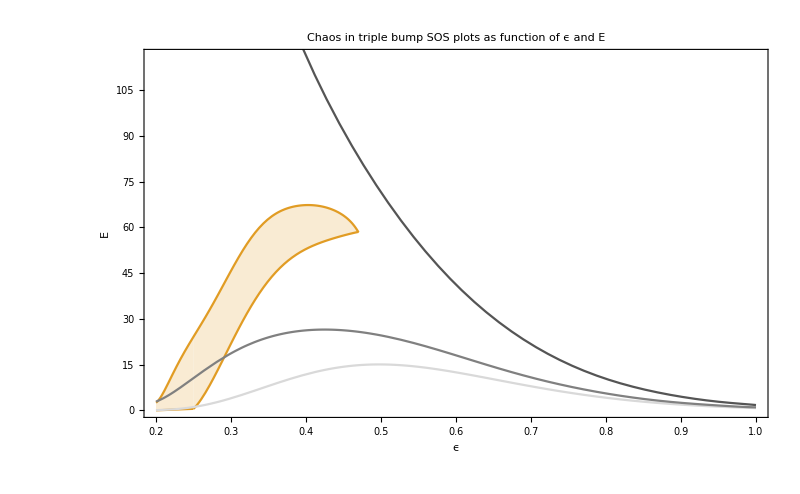

```mathematica
(*list points and plot*)
chaosPts=Flatten[{{{0.4625,231},{0.25,1}},Table[{0.4,i},{i,210,260,10}],Table[{0.45,i},{i,230,250,10}],Table[{0.35,i},{i,180,250,10}],Table[{0.3,i},{i,{90,100,110,120,130,170,180}}],Table[{0.25,i},{i,10,90,10}],Table[{0.2,i},{i,{10}}]},1];
integrablePts=Flatten[{{{0.25,0.2}},Table[{0.4,i},{i,{200,270,280,290,300}}],Table[{0.45,i},{i,{220,260}}],Table[{0.35,i},{i,120,170,10}],Table[{0.35,i},{i,260,280,10}],Table[{0.3,i},{i,{70,80,190,210,240,250,260,270}}],Table[{0.25,i},{i,100,130,10}],Table[{0.2,i},{i,{20,30,60}}],Table[{0.475,i},{i,{226,230,232,234,238,242,246}}]},1];
chaosPlot=ListPlot[{integrablePts,chaosPts},PlotRange->{{0.2,1.0},{0,400}},PlotStyle->PointSize[0.01],Frame->True,FrameLabel->{{"E",None},{"ϵ",None}},PlotLegends->{Placed[{"Integrable/Mixed","Chaos"},{0.8,0.8}]},LabelStyle->Directive[16],PlotLabel->"Chaos in triple bump SOS plots as function of ϵ and E",ImageSize->800];
chaosBorderTop[x_]=Fit[{{0.2,10},{0.225,52.5},{0.25,95},{0.275,137.5},{0.3,180},{0.35,250},{0.375,260},{0.4,268},{0.425,263},{0.45,253},{0.47,231}},Table[x^n,{n,0,9}],x];
chaosBorderBot[x_]=Fit[{(*{0.2,0},{0.2125,0.25},{0.225,0.5},{0.2375,0.75},*)(*{0.2,-200},*){0.25,1},{0.275,42},{0.3,84},{0.325,128},{0.35,175},{0.4,205},{0.425,221},{0.45,228},{0.47,231}},Table[x^n,{n,0,5}],x];
scaling=0.842*3/10;
borderPlot=Plot[{chaosBorderTop[x]*scaling,
Piecewise[{{chaosBorderBot[x]*scaling,x>0.25},{10(x-0.2),x<0.25}}]
},{x,0.2,0.47},PlotStyle->{(ColorData[97,"ColorList"][[2]])},Filling->{1->{2}},PlotRange->{{0.2,1.0},{0,116}},Frame->True,FrameLabel->{{"E",None},{"ϵ",None}},LabelStyle->Directive[16],PlotLabel->"Chaos in triple bump SOS plots as function of ϵ and E",ImageSize->800,
PlotLegends->Placed[SwatchLegend[{ColorData[97,"ColorList"][[2]]},{"Fully chaotic"},LegendMarkers->chaosLegendMark],{0.78,0.62}]];
(*borderBot=Plot[{chaosBorderBot[x]},{x,0.25,0.47},PlotStyle->{(ColorData[97,"ColorList"][[2]])}];*)
Show[(*chaosPlot,*)borderPlot(*borderPlotExtra*),saddlePeakPlot]
```

```mathematica
gold=ColorData[97,"ColorList"][[2]];
chaosLegendMark=Graphics[{EdgeForm[{Thickness[0.007],gold}],gold,Opacity[0.3],Rectangle[{0,0},{1,1}]}]
```

-Graphics-

Evidence of above
WARNING: Before a simulation, if you are CHANGING ϵ, also CHANGE THE TRENCH

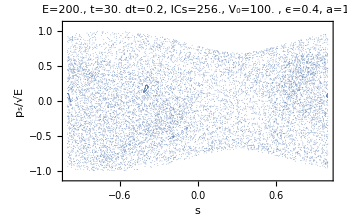
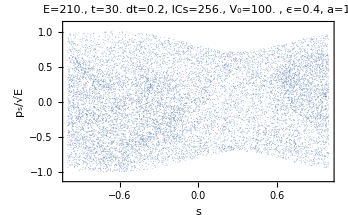
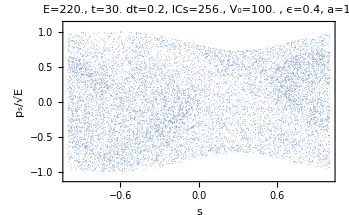
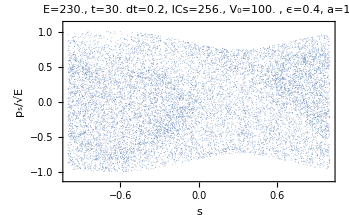
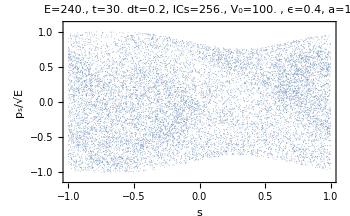
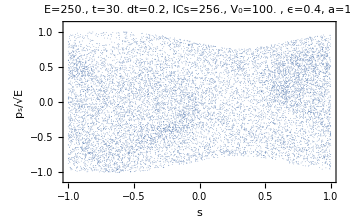
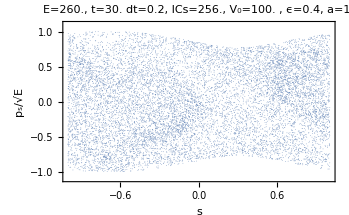
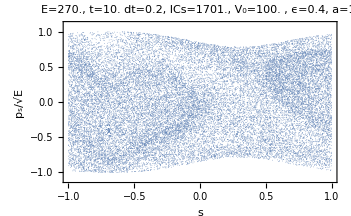
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}(*E=232 is a single bifurcation of E=230 here*)
{-Graphics-,-Graphics-}(*E=230 is unstable, E=232 is stable here*)
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

WRONG POINTS AND PLOTS -- done for center bump = 400 (instead of off-center)

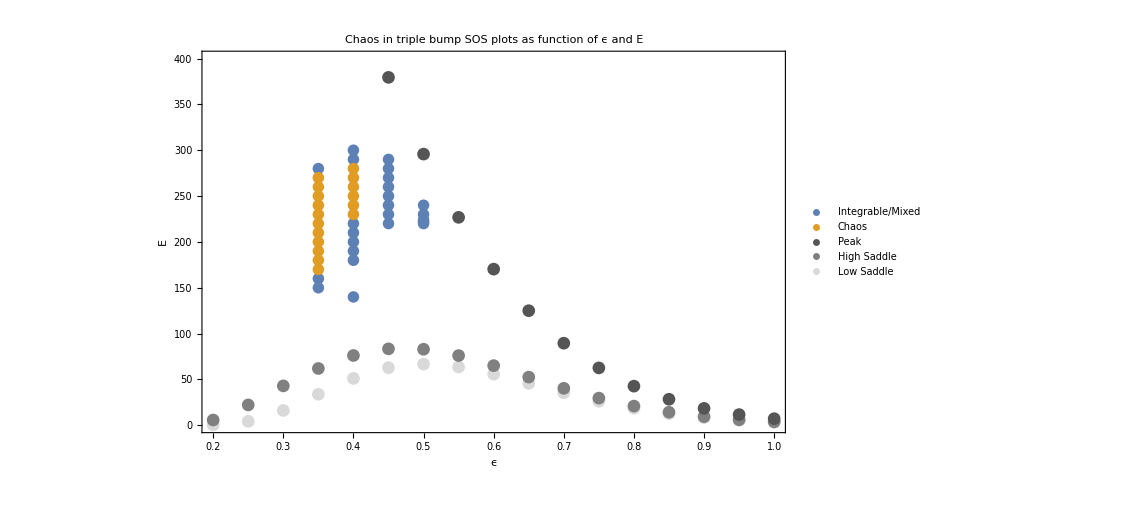

```mathematica
chaosPts=Flatten[{{},Table[{0.4,i},{i,{230,240,250,260,270,280}}],Table[{0.45,i},{i,{}}],Table[{0.35,i},{i,170,270,10}]},1];
integrablePts=Flatten[{{},Table[{0.4,i},{i,{140,180,190,200,210,220,290,300}}],Table[{0.45,i},{i,{220,230,240,250,260,270,280,290}}],Table[{0.5,i},{i,{220,222,224,230,240}}],Table[{0.35,i},{i,{150,160,280}}]},1];
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

#### Single Bump region of chaos [**Forgot to use height 400 instead of 100 here]

List of points (collected from everywhere) in ϵ-V0 space collected into a list of fully-chaotic SOSs and at-least-partially-integrable SOSs
The parameters that can be changed before a simulation are: ϵ,a,V0,E,tmax,dt. The variables which will change automatically due to the shape of the lattice (i.e. the phase space scale on which the dynamics play out) are x,y,px,py. We know tmax and dt just affect the number of points collected during the simulation, not the resulting SOS shape. And we know E∝1/V0 (ignoring px,py) so we set one (either one) constant. So to take an existing plot and categorize it here, we (1) scale E and V0 by the same amount to get E=100, then (2) scale ϵ,a,V0 appropriately (ϵ by β, a by β, V0 by β^2) to get a=1.0. The resulting ϵ and V0 go on the plot.

Useful scaling property: E->β^2 E and V0->β^2 V0 need only t->t/β and dt->dt/β to cancel. So plots with the wrong V0 can be scaled at no cost.

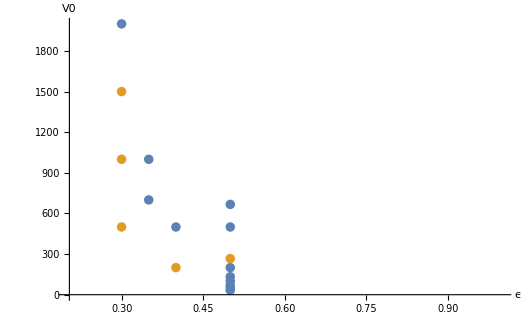

```mathematica
(*ϵ,V0 version - ignore*)
(*chaosPts={{0.5,267},{0.4,200},{0.3,500},{0.3,1000},{0.3,1500}};
integrablePts={{0.5,200},{0.5,133},{0.5,100},{0.5,67},{0.5,50},{0.5,33},{0.5,500},{0.5,667},{0.2,10000},{0.4,500},{0.3,2000},{0.35,1000},{0.35,700}};
ListPlot[{integrablePts,chaosPts},PlotRange->{{0.2,1.0},{0,2000}},AxesLabel->{"ϵ","V0"}]*)
```

```mathematica
(*f[{x_,y_}]:={x,100.^2/y}
chaosPts=Round[f/@chaosPts,0.01]
integrablePts=Round[f/@integrablePts,0.01]*)
```

```mathematica
V0=30;
a=1.0;
Clear[ϵ];
```

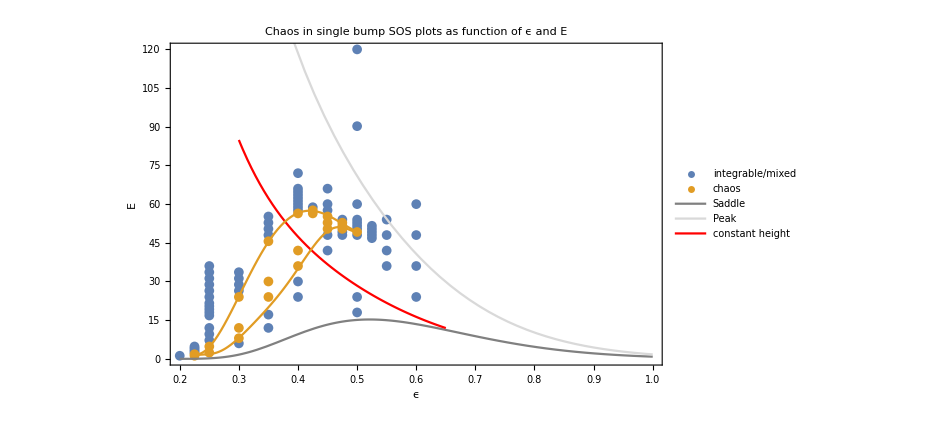

```mathematica
(*ϵ,E version*)
scaling=0.3*4;(*due to V0=100->30 and originally missing factor of 4 in Vth*)
scalingM={{1,0},{0,scaling}};
chaosPts=Map[scalingM.#&,Flatten[{{{0.3,20.},{0.3,10.},{0.3,6.67},{0.4,35},{0.35,25},{0.35,20},{0.4,30},{0.45,42},{0.45,44},{0.45,46},{0.5,41},{0.35,38},{0.425,47},{0.425,48},{0.4,47}},Table[{0.475,i},{i,42,44,1}],Table[{0.25,i},{i,2,4,2}],Table[{0.225,i},{i,1,1.5,0.5}]},1]];
integrablePts=Map[scalingM.#&,Flatten[{{{0.5,50.},{0.5,75.19},{0.5,100.},{0.5,149.25},{0.5,200.},{0.5,303.},{0.5,20.},{0.5,15},{0.2,1.},{0.4,20.},{0.3,5.},{0.35,10.},{0.35,14.29},{0.4,25},{0.45,35},{0.45,40},{0.45,48},{0.45,50},{0.45,55},{0.475,40},{0.475,41},{0.475,45},{0.425,49}},Table[{0.6,i},{i,20,50,10}],Table[{0.55,i},{i,30,45,5}],Delete[Table[{0.5,i},{i,40,45,1}],2],Table[{0.525,i},{i,39,43}],Table[{0.4,i},{i,55,60,5}],Table[{0.35,i},{i,40,46,2}],Table[{0.25,i},{i,14,18,1}],Table[{0.25,i},{i,20,30,2}],Table[{0.25,i},{i,6,10,2}],Table[{0.3,i},{i,22,28,2}],Table[{0.225,i},{i,2,4,0.5}],Table[{0.4,i},{i,48,54,1}]},1]];
chaosPlot=ListPlot[{integrablePts,chaosPts},PlotRange->{{0.2,1.0},{0,120}},PlotStyle->PointSize[0.01],Frame->True,FrameLabel->{{"E",None},{"ϵ",None}},PlotLegends->{Placed[{"integrable/mixed","chaos"},{0.8,0.8}]},LabelStyle->Directive[16],PlotLabel->"Chaos in single bump SOS plots as function of ϵ and E",ImageSize->700];

Vth[x_,y_]:=4((V0 EllipticTheta[3,-(π x)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))] EllipticTheta[3,-(π y)/(2 a),ⅇ^(-(π^2 ϵ^2)/(2 a^2))])/(4 a^2)-(V0 EllipticTheta[3,-π/2,ⅇ^(-(π^2 ϵ^2)/(2 a^2))]^2)/(4 a^2))
saddlePlot=Plot[Vth[0,a],{ϵ,0.2,1.0},PlotStyle->Gray,PlotLegends->Placed[LineLegend[{Gray,LightGray,Red},{"Saddle","Peak","constant height"},LabelStyle->Directive[16]],{0.8,0.6}]];
peakPlot=Plot[Vth[0,0],{ϵ,0.2,1.0},PlotStyle->LightGray];
pathPlot=Plot[2/5*Vth[0,0],{ϵ,0.3,0.65},PlotStyle->Red];
chaosBorderTop[x_]=scaling*Fit[{{0.225,1.5},{0.25,4},{0.3,20},{0.35,38},{0.4,47},{0.425,48},{0.45,46},{0.475,44},{0.5,41}},Table[x^n,{n,0,5}],x];
chaosBorderBot[x_]=scaling*Fit[{{0.225,1},{0.25,1},{0.275,4},{0.3,6.67},{0.325,10},{0.35,18},{0.375,23},{0.4,28},{0.425,36},{0.45,42},{0.475,42},{0.5,41}},Table[x^n,{n,0,7}],x];
border=Plot[{chaosBorderTop[x],chaosBorderBot[x]},{x,0.225,0.5},PlotStyle->{(ColorData[97,"ColorList"][[2]])}];
Show[chaosPlot,saddlePlot,peakPlot,pathPlot,border]
```

Evidence of above

```mathematica
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
```

This one best tells the story of the s=0 fixed point destabilizing, bifurcating, disappearing into total chaos, then stabilizing again.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

«1 more identical outputs»

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(I only just realized I’ve been normalizing wrong -- all plots have had px/√EnMod with Enmod=30 for all. This doesn’t change the qualitative results of any of the plots, and I’ve fixed this going forward (so EnMod=En), but I can’t use any plots above this line in the paper (not that I wanted to).)

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Received errors such as Greater::nord: "Invalid comparison with (small complex number) attempted.", probably for lowest energies*)
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

(N.B.: This was moved to file ‘For Linda - Region of chaos draft.nb’ and edited/expanded.)

Explaining what determines the range of total chaos at a given value of ϵ:

Below is a plot of the range of ϵ (bump width parameter) and E (trajectory energy parameter) for which the surface of section is entirely chaotic (neglecting microscopically small stable islands). The main aspects to notice about it are that total chaos can only occur within a certain range of ϵ (about 0.225<ϵ<0.5), and that it is tightly bounded in E. It turns out that the energy range of total chaos at a given ϵ is entirely dependent on the stability of a single orbit.

For most values of ϵ, the same basic evolution happens as you increase E from the saddle energy to the peak energy. Starting at the saddle energy, the main stable orbit is at (x,px)=(0,0) (see plots below), which is a straight line running vertically through the minimum and a saddle (an equivalent horizontally travelling orbit exists as well) [I can add pictures of these as well]. As energy rises above the saddle, this orbit destabilizes and bifurcates, and the two new stable orbits drift away from x=0 while still maintaining px=0 (the equivalent horizontal orbits have bifurcations along x=0, aka s=1). Eventually these descend into chaos. Also eventually, the original orbit at (x,px)=(0,0) re-stabilizes and grows until it dominates the dynamics. The important question is which comes first: the bifurcation’s descent into chaos, or the re-stabilization of the original orbit? If the former happens first, then a regime of total chaos is enjoyed before the latter occurs; but if instead the re-stabilization happens while the bifurcation is still present, as is the case for large enough ϵ, then no regime of total chaos exists.

To illustrate the difference between ϵ<0.5 (some total chaos) and ϵ>0.5 (no total chaos), here’s two examples. The first is forϵ=0.45, and shows the original stable orbit, bifurcation, and descent into chaos as E goes 20->45. Then at E=50 the original orbit becomes stable again and only grows bigger for further increase of E. Further investigation gave the points on the above plot, which indicate that for ϵ=0.45 total chaos exists for 42≲E≲46.

```mathematica
(*these plots should have labels "x" and "px" instead of "s" and "ps", and they were all accidentally stretched or compressed vertically when they were made -- I will fix all of this before putting anything in the paper, if this goes in the paper*)
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,}
```

The second example is for ϵ=0.525. Just a single plot shows that the bifurcation and the re-stabilization are both present at the same energy. Just one such plot is evidence that no regime of total chaos can exist for this value of ϵ.

Demonstrating that E, V0, t, and dt can be scaled together as E->β^2 E, V0->β^2 V0, t->t/β, dt->dt/β (though this property may no longer be useful since I’m using E instead of V0):

```mathematica
-Graphics--Graphics-
-Graphics--Graphics-
```